```mathematica
w1=7;w2=11;h1=7;h2=12;
```

```mathematica
θ1=ArcTan[h2/w1];θ2=ArcTan[h1/w2];θ3=ArcTan[h1/w1];
```

```mathematica
δh=2*h1+h2+5;δw=-w1-w2-4;
```

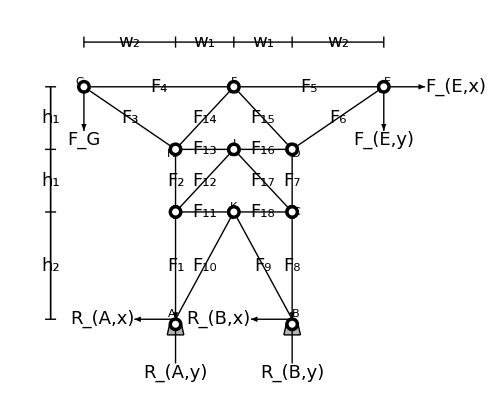

```mathematica
Module[{FEx,FEy,FG,RAx,RAy,RB,scale,truss,measurements},
FEx=5;FEy=FEx;FG=FEx;
RAx=FEx;RAy=FEx;RB=FEx;

scale[F_]:=3+10*Rescale[Abs@F,{0,25.7}];
colC=RGBColor[0,0.6,0];colT=RGBColor[1,0,0.25];

truss=Graphics[{Thick,
(*SUPPORTS*)
{Thick,{GrayLevel@0.7,Disk[{#*w1,-0.75},0.75],Polygon[{{#*w1-0.75,-0.75/2},{#*w1+0.75,-0.75/2},{#*w1+1,-1.75},{#*w1-1,-1.75}}]},
Line[{{#*w1-0.75,-0.75},{#*w1-1,-1.75}}],
Line[{{#*w1+0.75,-0.75},{#*w1+1,-1.75}}],
Line[{{#*w1-1,-1.75},{#*w1+1,-1.75}}],
Line@Table[{i,√(0.75^2-(i-#*w1)^2)-0.75},{i,#*w1-0.75,#*w1+0.75,0.1}]}&/@{-1,1},

(*REACTION FORCES*)
{Arrowheads@0.04,
Arrow[{{-w1,-scale[RAy]},{-w1,-0.5}}],Arrow[{{-w1,0},{-w1-scale[RAx],0}}],
Text[Style[Subscript[Style["R",Italic],Row@{"A,",Style[#1,Italic]}],18],#2,#3]&@@@{{"x",{-w1-scale[RAx],0},{1,0}},{"y",{-w1,-scale[RAy]},{0,1}}},
Arrow[{{w1,-scale[RB]},{w1,-0.5}}],Arrow[{{w1,0},{w1-scale[RAx],0}}],
Text[Style[Subscript[Style["R",Italic],Row@{"B,",Style[#1,Italic]}],18],#2,#3]&@@@{{"x",{w1-scale[RAx],0},{1,0}},{"y",{w1,-scale[RB]},{0,1}}},

Arrow[{{-w1-w2,2*h1+h2},{-w1-w2,2*h1+h2-scale[FG]}}],
Text[Style[Subscript[Style["F",Italic],"G"],18],{-w1-w2,2*h1+h2-scale[FG]},{0,1}],
Arrow[{{w1+w2,2*h1+h2},{w1+w2,2*h1+h2-scale[FEy]}}],
Arrow[{{w1+w2,2*h1+h2},{w1+w2+scale[FEx],2*h1+h2}}],
Text[Style[Subscript[Style["F",Italic],Row@{"E,",Style[#1,Italic]}],18],#2,#3]&@@@{{"x",{w1+w2+scale[FEx],2*h1+h2},{-1,0}},{"y",{w1+w2,2*h1+h2-scale[FEy]},{0,1}}}},

{Arrowheads@{-0.04,0.04},
Arrow[{{-w1,0},{-w1,h2}}],Arrow[{{-w1,h2},{-w1,h1+h2}}],Arrow[{{-w1,h1+h2},{-w1-w2,2*h1+h2}}],Arrow[{{-w1,h2},{0,h2}}],Arrow[{{-w1,h1+h2},{0,h1+h2}}],Arrow[{{0,h1+h2},{w1,h1+h2}}],
Arrow[{{0,h1+h2},{w1,h2}}],Arrow[{{w1,h2},{w1,h1+h2}}],Arrow[{{w1,h1+h2},{w1+w2,2*h1+h2}}],Arrow[{{w1,h1+h2},{0,2*h1+h2}}],Arrow[{{w1,0},{w1,h2}}]},

{Arrowheads@{{0.04,0.315},{-0.04,0.675}},
Arrow[{{-w1,0},{0,h2}}],Arrow[{{0,h2},{w1,h2}}],Arrow[{{-w1,h2},{0,h1+h2}}],Arrow[{{-w1,h1+h2},{0,2*h1+h2}}],Arrow[{{-w1-w2,2*h1+h2},{0,2*h1+h2}}],Arrow[{{0,2*h1+h2},{w1+w2,2*h1+h2}}]},

Line[{{0,h2},{w1,0}}],

(*JOINTS*)
Text[Framed[Style[Row@{" ",#1," "},16],RoundingRadius->20,FrameMargins->Tiny],#2,#3]&@@@{{"A",{-w1,0},{2,-1}},{"B",{w1,0},{-2,-1}},{"C",{w1,h2},{-2,0}},{"D",{w1,h1+h2},{-2,1}},{"E",{w1+w2,2*h1+h2},{-1,-1.5}},{"F",{0,2*h1+h2},{0,-1.5}},{"G",{-w1-w2,2*h1+h2},{1,-1.5}},{"H",{-w1,h1+h2},{2,1}},{" I ",{-w1,h2},{2,0}},{"J",{0,h1+h2},{0,-1.5}},{"K",{0,h2},{0,-1.5}}},

(*FORCES*)
Text[Style[Subscript[Style["F",Italic],#1],18,Background->White],#2]&@@@{{1,{-w1,h2/2}},{2,{-w1,h2+h1/2}},{3,{-w1-w2/2,1.5*h1+h2}},{4,{-(w1+w2)/2,2*h1+h2}},{5,{(w1+w2)/2,2*h1+h2}},{6,{w1+w2/2,1.5*h1+h2}},{7,{w1,h1/2+h2}},{8,{w1,h2/2}},{9,{w1/2,h2/2}},{10,{-w1/2,h2/2}},{11,{-w1/2,h2}},{12,{-w1/2,h1/2+h2}},{13,{-w1/2,h1+h2}},{14,{-w1/2,1.5*h1+h2}},{15,{w1/2,1.5*h1+h2}},{16,{w1/2,h1+h2}},{17,{w1/2,h1/2+h2}},{18,{w1/2,h2}}}
}];


measurements=Graphics[{
(*MEASUREMENTS*)
{Line[{{0,δh},{#*w1,δh}}],
Line[{{#*(w1+w2),δh},{#*w1,δh}}],
Line[{{δw,0},{δw,h2}}],Line[{{δw,h2},{δw,h1+h2}}],Line[{{δw,h1+h2},{δw,2*h1+h2}}]
}&/@{-1,1},
Line[{{#,0.98*δh},{#,1.02*δh}}]&/@{-w1-w2,-w1,0,w1,w1+w2},
Line[{{0.97*δw,#},{1.03*δw,#}}]&/@{0,h2,h1+h2,2*h1+h2},

{Text[Style[Subscript[Style["w",Italic],1],18,Background->White],{#*w1/2,δh}],
Text[Style[Subscript[Style["w",Italic],2],18,Background->White],{#*(w1+w2/2),δh}]}&/@{-1,1},
Text[Style[Subscript[Style["h",Italic],2],18,Background->White],{δw,h2/2}],
Text[Style[Subscript[Style["h",Italic],1],18,Background->White],{δw,h2+#*h1}]&/@{0.5,1.5},

(*(*ANGLES*)
{Thin,
Circle[{-w1,0},2,{0,θ1}],Text[Style[Subscript[Style["θ",Italic],1],17],{-w1,0},{-3,-1}]
},
*)
{PointSize@0.02,Point@#,White,PointSize@0.01,Point@#}&/@{{-w1,-0.56},{w1,-0.56},{-w1,h2},{w1,h2},{-w1,h1+h2},{w1,h1+h2},{-w1-w2,2*h1+h2},{w1+w2,2*h1+h2},{0,h2},{0,h1+h2},{0,2*h1+h2}}
}];

Show[truss,measurements,ImageSize->500]
]
```

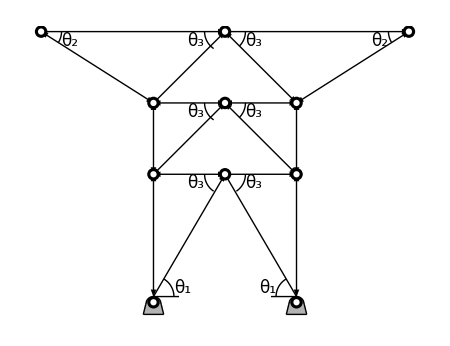

```mathematica
Module[{r,FEx,FEy,FG,RAx,RAy,RB,scale,truss},
r=2;
FEx=5;FEy=FEx;FG=FEx;
RAx=FEx;RAy=FEx;RB=FEx;

scale[F_]:=3+10*Rescale[Abs@F,{0,25.7}];
colC=RGBColor[0,0.6,0];colT=RGBColor[1,0,0.25];

truss=Graphics[{Thick,
(*SUPPORTS*)
{Thick,{GrayLevel@0.7,Disk[{#*w1,-0.75},0.75],Polygon[{{#*w1-0.75,-0.75/2},{#*w1+0.75,-0.75/2},{#*w1+1,-1.75},{#*w1-1,-1.75}}]},
Line[{{#*w1-0.75,-0.75},{#*w1-1,-1.75}}],
Line[{{#*w1+0.75,-0.75},{#*w1+1,-1.75}}],
Line[{{#*w1-1,-1.75},{#*w1+1,-1.75}}],
Line@Table[{i,√(0.75^2-(i-#*w1)^2)-0.75},{i,#*w1-0.75,#*w1+0.75,0.1}]}&/@{-1,1},

{Arrowheads@{-0.04,0.04},
Arrow[{{-w1,0},{-w1,h2}}],Arrow[{{-w1,h2},{-w1,h1+h2}}],Arrow[{{-w1,h1+h2},{-w1-w2,2*h1+h2}}],Arrow[{{-w1,h2},{0,h2}}],Arrow[{{-w1,h1+h2},{0,h1+h2}}],Arrow[{{0,h1+h2},{w1,h1+h2}}],
Arrow[{{0,h1+h2},{w1,h2}}],Arrow[{{w1,h2},{w1,h1+h2}}],Arrow[{{w1,h1+h2},{w1+w2,2*h1+h2}}],Arrow[{{w1,h1+h2},{0,2*h1+h2}}],Arrow[{{w1,0},{w1,h2}}]},

{Arrowheads@{{0.04,0.315},{-0.04,0.675}},
Arrow[{{-w1,0},{0,h2}}],Arrow[{{0,h2},{w1,h2}}],Arrow[{{-w1,h2},{0,h1+h2}}],Arrow[{{-w1,h1+h2},{0,2*h1+h2}}],Arrow[{{-w1-w2,2*h1+h2},{0,2*h1+h2}}],Arrow[{{0,2*h1+h2},{w1+w2,2*h1+h2}}]},

Line[{{0,h2},{w1,0}}],

(*ANGLES*)
{Thin,
Circle[{-w1,0},r,{0,θ1}],Line[{{-w1,0},{-w1+r+0.5,0}}],Text[Style[Subscript[Style["θ",Italic],1],17],{-w1+r,0},{-1,-1}],
Circle[{w1,0},r,{180°,180°-θ1}],Line[{{w1,0},{w1-2.5,0}}],Text[Style[Subscript[Style["θ",Italic],1],17],{w1-r,0},{1,-1}],

Circle[{0,h2},r,{180°,180°+1.25*θ3}],Text[Style[Subscript[Style["θ",Italic],3],17],{-r,h2},{1,1.5}],
Circle[{0,h2},r,{0°,-1.25*θ3}],Text[Style[Subscript[Style["θ",Italic],3],17],{r,h2},{-1,1.5}],

Circle[{0,h1+h2},r,{180°,180°+1.25*θ3}],Text[Style[Subscript[Style["θ",Italic],3],17],{-r,h1+h2},{1,1.5}],
Circle[{0,h1+h2},r,{0°,-θ3}],Text[Style[Subscript[Style["θ",Italic],3],17],{r,h1+h2},{-1,1.5}],

Circle[{0,2*h1+h2},r,{180°,180°+1.25*θ3}],Text[Style[Subscript[Style["θ",Italic],3],17],{-r,2*h1+h2},{1,1.5}],
Circle[{0,2*h1+h2},r,{0°,-θ3}],Text[Style[Subscript[Style["θ",Italic],3],17],{r,2*h1+h2},{-1,1.5}],

Circle[{-w1-w2,2*h1+h2},r,{-θ2,0°}],Text[Style[Subscript[Style["θ",Italic],2],17],{-w1-w2+r,2*h1+h2},{-1.2,1}],
Circle[{w1+w2,2*h1+h2},r,{180°,180°+θ2}],Text[Style[Subscript[Style["θ",Italic],2],17],{w1+w2-r,2*h1+h2},{1.2,1}]
},

{PointSize@0.02,Point@#,White,PointSize@0.01,Point@#}&/@{{-w1,-0.56},{w1,-0.56},{-w1,h2},{w1,h2},{-w1,h1+h2},{w1,h1+h2},{-w1-w2,2*h1+h2},{w1+w2,2*h1+h2},{0,h2},{0,h1+h2},{0,2*h1+h2}}
},ImageSize->450]
]
```